```mathematica
Eq1 = (M+2 Mw+2 Iw/r^2) x'[t]+M l α''[t] Cos[α[t]]-M l (α'[t])^2 Sin[α[t]]== Tl[t]/r+Tr[t]/r
```

(M+2 Mw+(2 Iw)/r^2) x'[t]-l M Sin[α[t]] α'[t]^2+l M Cos[α[t]] α''[t]==Tl[t]/r+Tr[t]/r

```mathematica
Eq2 =(Ip+2 (Mw+Iw/r^2) d^2) θ''[t]==2 d (Tl[t]/r-Tr[t]/r)
```

(Ip+2 d^2 (Mw+Iw/r^2)) θ''[t]==2 d (Tl[t]/r-Tr[t]/r)

```mathematica
Eq3 = M l x'[t] Cos[α[t]]+(M l^2+Ix) α''[t]-m g l Sin[α[t]]==0
```

-g l m Sin[α[t]]+l M Cos[α[t]] x'[t]+(Ix+l^2 M) α''[t]==0

```mathematica
model = StateSpaceModel[{Eq1,Eq2,Eq3},{{x[t],0},{α[t],0},{α'[t],0},{θ[t],0},{θ'[t],0}},{Tr[t],Tl[t]}, {x[t],theta[t],alpha[t]},t]
```

0(g l m (-Ip l M-2 d^2 l M Mw-(2 d^2 Iw l M)/r^2))/((Ip+2 d^2 (Mw+Iw/r^2)) (Ix M+2 Ix Mw+2 l^2 M Mw+(2 Iw Ix)/r^2+(2 Iw l^2 M)/r^2))000((Ix+l^2 M) (Ip+2 d^2 Mw+(2 d^2 Iw)/r^2))/((Ip+2 d^2 (Mw+Iw/r^2)) (Ix M+2 Ix Mw+2 l^2 M Mw+(2 Iw Ix)/r^2+(2 Iw l^2 M)/r^2) r)((Ix+l^2 M) (Ip+2 d^2 Mw+(2 d^2 Iw)/r^2))/((Ip+2 d^2 (Mw+Iw/r^2)) (Ix M+2 Ix Mw+2 l^2 M Mw+(2 Iw Ix)/r^2+(2 Iw l^2 M)/r^2) r)00100000(g l m (M+2 Mw+(2 Iw)/r^2))/(Ix M+2 Ix Mw+2 l^2 M Mw+(2 Iw Ix)/r^2+(2 Iw l^2 M)/r^2)000(-Ip l M-2 d^2 l M Mw-(2 d^2 Iw l M)/r^2)/((Ip+2 d^2 (Mw+Iw/r^2)) (Ix M+2 Ix Mw+2 l^2 M Mw+(2 Iw Ix)/r^2+(2 Iw l^2 M)/r^2) r)(-Ip l M-2 d^2 l M Mw-(2 d^2 Iw l M)/r^2)/((Ip+2 d^2 (Mw+Iw/r^2)) (Ix M+2 Ix Mw+2 l^2 M Mw+(2 Iw Ix)/r^2+(2 Iw l^2 M)/r^2) r)0000-(-Ix M-2 Ix Mw-2 l^2 M Mw-(2 Iw Ix)/r^2-(2 Iw l^2 M)/r^2)/(Ix M+2 Ix Mw+2 l^2 M Mw+(2 Iw Ix)/r^2+(2 Iw l^2 M)/r^2)0000000-(2 d)/((Ip+2 d^2 (Mw+Iw/r^2)) r)(2 d)/((Ip+2 d^2 (Mw+Iw/r^2)) r)100000000000000000000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2351FalseFalseFalseAutomaticNone,{{x[t],0},{α[t],0},x_1,{θ[t],0},x_2},{{Tr[t],0},{Tl[t],0}},Automatic,t

```mathematica
0100000000-(g l m (-Ip l M-2 d^2 l M Mw-(2 d^2 Iw l M)/r^2))/((Ip+2 d^2 (Mw+Iw/r^2)) (-Im M-2 Im Mw-2 l^2 M Mw-(2 Im Iw)/r^2-(2 Iw l^2 M)/r^2))000-((Im+l^2 M) (Ip+2 d^2 Mw+(2 d^2 Iw)/r^2))/((Ip+2 d^2 (Mw+Iw/r^2)) (-Im M-2 Im Mw-2 l^2 M Mw-(2 Im Iw)/r^2-(2 Iw l^2 M)/r^2) r)-((Im+l^2 M) (Ip+2 d^2 Mw+(2 d^2 Iw)/r^2))/((Ip+2 d^2 (Mw+Iw/r^2)) (-Im M-2 Im Mw-2 l^2 M Mw-(2 Im Iw)/r^2-(2 Iw l^2 M)/r^2) r)000-(Im M+2 Im Mw+2 l^2 M Mw+(2 Im Iw)/r^2+(2 Iw l^2 M)/r^2)/(-Im M-2 Im Mw-2 l^2 M Mw-(2 Im Iw)/r^2-(2 Iw l^2 M)/r^2)000000-(g l m (M+2 Mw+(2 Iw)/r^2))/(-Im M-2 Im Mw-2 l^2 M Mw-(2 Im Iw)/r^2-(2 Iw l^2 M)/r^2)000-(-Ip l M-2 d^2 l M Mw-(2 d^2 Iw l M)/r^2)/((Ip+2 d^2 (Mw+Iw/r^2)) (-Im M-2 Im Mw-2 l^2 M Mw-(2 Im Iw)/r^2-(2 Iw l^2 M)/r^2) r)-(-Ip l M-2 d^2 l M Mw-(2 d^2 Iw l M)/r^2)/((Ip+2 d^2 (Mw+Iw/r^2)) (-Im M-2 Im Mw-2 l^2 M Mw-(2 Im Iw)/r^2-(2 Iw l^2 M)/r^2) r)00000100000000(2 d (Im M+2 Im Mw+2 l^2 M Mw+(2 Im Iw)/r^2+(2 Iw l^2 M)/r^2))/((Ip+2 d^2 (Mw+Iw/r^2)) (-Im M-2 Im Mw-2 l^2 M Mw-(2 Im Iw)/r^2-(2 Iw l^2 M)/r^2) r)-(2 d (Im M+2 Im Mw+2 l^2 M Mw+(2 Im Iw)/r^2+(2 Iw l^2 M)/r^2))/((Ip+2 d^2 (Mw+Iw/r^2)) (-Im M-2 Im Mw-2 l^2 M Mw-(2 Im Iw)/r^2-(2 Iw l^2 M)/r^2) r)100000000000000000000000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5$CellContext`stname6Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2361FalseFalseFalseAutomaticNone,{{x[t],0},Subscript[x, 1],{α[t],0},Subscript[x, 2],{θ[t],0},Subscript[x, 3]},{{Tr[t],0},{Tl[t],0}},Automatic,t
```

```mathematica
Normal[model]
```

{{{0,0,0,1,0,0},{0,0,0,0,-(-((Im+l^2 M) (M+2 Mw+(2 Iw)/r^2))+l^2 M^2 cos[0]^2)/((Im+l^2 M) (M+2 Mw+(2 Iw)/r^2)-l^2 M^2 cos[0]^2),0},{0,0,0,0,0,-(-((Im+l^2 M) (M+2 Mw+(2 Iw)/r^2))+l^2 M^2 cos[0]^2)/((Im+l^2 M) (M+2 Mw+(2 Iw)/r^2)-l^2 M^2 cos[0]^2)},{0,0,-(g l^2 m M cos[0] sin'[0])/((Im+l^2 M) (M+2 Mw+(2 Iw)/r^2)-l^2 M^2 cos[0]^2),0,0,0},{0,0,0,0,0,0},{0,0,(g l m (M+2 Mw+(2 Iw)/r^2) sin'[0])/((Im+l^2 M) (M+2 Mw+(2 Iw)/r^2)-l^2 M^2 cos[0]^2),0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{-((Im+l^2 M) (-Ip-2 d^2 Mw-(2 d^2 Iw)/r^2))/((Ip+2 d^2 (Mw+Iw/r^2)) r ((Im+l^2 M) (M+2 Mw+(2 Iw)/r^2)-l^2 M^2 cos[0]^2)),-((Im+l^2 M) (-Ip-2 d^2 Mw-(2 d^2 Iw)/r^2))/((Ip+2 d^2 (Mw+Iw/r^2)) r ((Im+l^2 M) (M+2 Mw+(2 Iw)/r^2)-l^2 M^2 cos[0]^2)),-((Im+l^2 M) (-Ip-2 d^2 Mw-(2 d^2 Iw)/r^2))/((Ip+2 d^2 (Mw+Iw/r^2)) ((Im+l^2 M) (M+2 Mw+(2 Iw)/r^2)-l^2 M^2 cos[0]^2)),-((Im+l^2 M) (-Ip-2 d^2 Mw-(2 d^2 Iw)/r^2))/((Ip+2 d^2 (Mw+Iw/r^2)) ((Im+l^2 M) (M+2 Mw+(2 Iw)/r^2)-l^2 M^2 cos[0]^2))},{(2 d (-((Im+l^2 M) (M+2 Mw+(2 Iw)/r^2))+l^2 M^2 cos[0]^2))/((Ip+2 d^2 (Mw+Iw/r^2)) r ((Im+l^2 M) (M+2 Mw+(2 Iw)/r^2)-l^2 M^2 cos[0]^2)),-(2 d (-((Im+l^2 M) (M+2 Mw+(2 Iw)/r^2))+l^2 M^2 cos[0]^2))/((Ip+2 d^2 (Mw+Iw/r^2)) r ((Im+l^2 M) (M+2 Mw+(2 Iw)/r^2)-l^2 M^2 cos[0]^2)),-(2 d (-((Im+l^2 M) (M+2 Mw+(2 Iw)/r^2))+l^2 M^2 cos[0]^2))/((Ip+2 d^2 (Mw+Iw/r^2)) ((Im+l^2 M) (M+2 Mw+(2 Iw)/r^2)-l^2 M^2 cos[0]^2)),(2 d (-((Im+l^2 M) (M+2 Mw+(2 Iw)/r^2))+l^2 M^2 cos[0]^2))/((Ip+2 d^2 (Mw+Iw/r^2)) ((Im+l^2 M) (M+2 Mw+(2 Iw)/r^2)-l^2 M^2 cos[0]^2))},{-(Ip l M cos[0]+2 d^2 l M Mw cos[0]+(2 d^2 Iw l M cos[0])/r^2)/((Ip+2 d^2 (Mw+Iw/r^2)) r ((Im+l^2 M) (M+2 Mw+(2 Iw)/r^2)-l^2 M^2 cos[0]^2)),-(Ip l M cos[0]+2 d^2 l M Mw cos[0]+(2 d^2 Iw l M cos[0])/r^2)/((Ip+2 d^2 (Mw+Iw/r^2)) r ((Im+l^2 M) (M+2 Mw+(2 Iw)/r^2)-l^2 M^2 cos[0]^2)),-(Ip l M cos[0]+2 d^2 l M Mw cos[0]+(2 d^2 Iw l M cos[0])/r^2)/((Ip+2 d^2 (Mw+Iw/r^2)) ((Im+l^2 M) (M+2 Mw+(2 Iw)/r^2)-l^2 M^2 cos[0]^2)),-(Ip l M cos[0]+2 d^2 l M Mw cos[0]+(2 d^2 Iw l M cos[0])/r^2)/((Ip+2 d^2 (Mw+Iw/r^2)) ((Im+l^2 M) (M+2 Mw+(2 Iw)/r^2)-l^2 M^2 cos[0]^2))}},{{1,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

```mathematica
ControllableModelQ[model]
```

True

```mathematica
ObservableModelQ[model]
```

False

```mathematica
FileNameJoin[{$UserBaseDirectory,"Applications"}]
```

C:\Users\ahmed\AppData\Roaming\Mathematica\Applications

```mathematica
Normal[model]//ToMatlab
```

ToMatlab[{{{0,1,0,0,0,0},{0,0,-(g l m (-Ip l M-2 d^2 l M Mw-(2 d^2 Iw l M)/r^2))/((Ip+2 d^2 (Mw+Iw/r^2)) (-Im M-2 Im Mw-2 l^2 M Mw-(2 Im Iw)/r^2-(2 Iw l^2 M)/r^2)),0,0,0},{0,0,0,-(Im M+2 Im Mw+2 l^2 M Mw+(2 Im Iw)/r^2+(2 Iw l^2 M)/r^2)/(-Im M-2 Im Mw-2 l^2 M Mw-(2 Im Iw)/r^2-(2 Iw l^2 M)/r^2),0,0},{0,0,-(g l m (M+2 Mw+(2 Iw)/r^2))/(-Im M-2 Im Mw-2 l^2 M Mw-(2 Im Iw)/r^2-(2 Iw l^2 M)/r^2),0,0,0},{0,0,0,0,0,1},{0,0,0,0,0,0}},{{0,0},{-((Im+l^2 M) (Ip+2 d^2 Mw+(2 d^2 Iw)/r^2))/((Ip+2 d^2 (Mw+Iw/r^2)) (-Im M-2 Im Mw-2 l^2 M Mw-(2 Im Iw)/r^2-(2 Iw l^2 M)/r^2) r),-((Im+l^2 M) (Ip+2 d^2 Mw+(2 d^2 Iw)/r^2))/((Ip+2 d^2 (Mw+Iw/r^2)) (-Im M-2 Im Mw-2 l^2 M Mw-(2 Im Iw)/r^2-(2 Iw l^2 M)/r^2) r)},{0,0},{-(-Ip l M-2 d^2 l M Mw-(2 d^2 Iw l M)/r^2)/((Ip+2 d^2 (Mw+Iw/r^2)) (-Im M-2 Im Mw-2 l^2 M Mw-(2 Im Iw)/r^2-(2 Iw l^2 M)/r^2) r),-(-Ip l M-2 d^2 l M Mw-(2 d^2 Iw l M)/r^2)/((Ip+2 d^2 (Mw+Iw/r^2)) (-Im M-2 Im Mw-2 l^2 M Mw-(2 Im Iw)/r^2-(2 Iw l^2 M)/r^2) r)},{0,0},{(2 d (Im M+2 Im Mw+2 l^2 M Mw+(2 Im Iw)/r^2+(2 Iw l^2 M)/r^2))/((Ip+2 d^2 (Mw+Iw/r^2)) (-Im M-2 Im Mw-2 l^2 M Mw-(2 Im Iw)/r^2-(2 Iw l^2 M)/r^2) r),-(2 d (Im M+2 Im Mw+2 l^2 M Mw+(2 Im Iw)/r^2+(2 Iw l^2 M)/r^2))/((Ip+2 d^2 (Mw+Iw/r^2)) (-Im M-2 Im Mw-2 l^2 M Mw-(2 Im Iw)/r^2-(2 Iw l^2 M)/r^2) r)}},{{1,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{0,0},{0,0},{0,0}}}]

```mathematica
<<ToMatlab`
Normal[model] //ToMatlab
```

ToMatlab::shdw: Symbol ToMatlab appears in multiple contexts {MatlabUtils`ToMatlab`,Global`}; definitions in context MatlabUtils`ToMatlab` may shadow or be shadowed by other definitions.

[[0,1,0,0,0,0;0,0,(-1).*g.*l.*m.*(Ip+2.*d.^2.*(Mw+Iw.*r.^(-2))).^( ...
  -1).*((-1).*Ip.*l.*M+(-2).*d.^2.*l.*M.*Mw+(-2).*d.^2.*Iw.*l.*M.* ...
  r.^(-2)).*((-1).*Im.*M+(-2).*Im.*Mw+(-2).*l.^2.*M.*Mw+(-2).*Im.* ...
  Iw.*r.^(-2)+(-2).*Iw.*l.^2.*M.*r.^(-2)).^(-1),0,0,0;0,0,0,(-1).*(( ...
  -1).*Im.*M+(-2).*Im.*Mw+(-2).*l.^2.*M.*Mw+(-2).*Im.*Iw.*r.^(-2)+( ...
  -2).*Iw.*l.^2.*M.*r.^(-2)).^(-1).*(Im.*M+2.*Im.*Mw+2.*l.^2.*M.*Mw+ ...
  2.*Im.*Iw.*r.^(-2)+2.*Iw.*l.^2.*M.*r.^(-2)),0,0;0,0,(-1).*g.*l.* ...
  m.*(M+2.*Mw+2.*Iw.*r.^(-2)).*((-1).*Im.*M+(-2).*Im.*Mw+(-2).* ...
  l.^2.*M.*Mw+(-2).*Im.*Iw.*r.^(-2)+(-2).*Iw.*l.^2.*M.*r.^(-2)).^( ...
  -1),0,0,0;0,0,0,0,0,1;0,0,0,0,0,0],[0,0;(-1).*(Im+l.^2.*M).*(Ip+ ...
  2.*d.^2.*(Mw+Iw.*r.^(-2))).^(-1).*(Ip+2.*d.^2.*Mw+2.*d.^2.*Iw.* ...
  r.^(-2)).*((-1).*Im.*M+(-2).*Im.*Mw+(-2).*l.^2.*M.*Mw+(-2).*Im.* ...
  Iw.*r.^(-2)+(-2).*Iw.*l.^2.*M.*r.^(-2)).^(-1).*r.^(-1),(-1).*(Im+ ...
  l.^2.*M).*(Ip+2.*d.^2.*(Mw+Iw.*r.^(-2))).^(-1).*(Ip+2.*d.^2.*Mw+ ...
  2.*d.^2.*Iw.*r.^(-2)).*((-1).*Im.*M+(-2).*Im.*Mw+(-2).*l.^2.*M.* ...
  Mw+(-2).*Im.*Iw.*r.^(-2)+(-2).*Iw.*l.^2.*M.*r.^(-2)).^(-1).*r.^( ...
  -1);0,0;(-1).*(Ip+2.*d.^2.*(Mw+Iw.*r.^(-2))).^(-1).*((-1).*Ip.*l.* ...
  M+(-2).*d.^2.*l.*M.*Mw+(-2).*d.^2.*Iw.*l.*M.*r.^(-2)).*((-1).*Im.* ...
  M+(-2).*Im.*Mw+(-2).*l.^2.*M.*Mw+(-2).*Im.*Iw.*r.^(-2)+(-2).*Iw.* ...
  l.^2.*M.*r.^(-2)).^(-1).*r.^(-1),(-1).*(Ip+2.*d.^2.*(Mw+Iw.*r.^( ...
  -2))).^(-1).*((-1).*Ip.*l.*M+(-2).*d.^2.*l.*M.*Mw+(-2).*d.^2.*Iw.* ...
  l.*M.*r.^(-2)).*((-1).*Im.*M+(-2).*Im.*Mw+(-2).*l.^2.*M.*Mw+(-2).* ...
  Im.*Iw.*r.^(-2)+(-2).*Iw.*l.^2.*M.*r.^(-2)).^(-1).*r.^(-1);0,0;2.* ...
  d.*(Ip+2.*d.^2.*(Mw+Iw.*r.^(-2))).^(-1).*((-1).*Im.*M+(-2).*Im.* ...
  Mw+(-2).*l.^2.*M.*Mw+(-2).*Im.*Iw.*r.^(-2)+(-2).*Iw.*l.^2.*M.*r.^( ...
  -2)).^(-1).*(Im.*M+2.*Im.*Mw+2.*l.^2.*M.*Mw+2.*Im.*Iw.*r.^(-2)+2.* ...
  Iw.*l.^2.*M.*r.^(-2)).*r.^(-1),(-2).*d.*(Ip+2.*d.^2.*(Mw+Iw.*r.^( ...
  -2))).^(-1).*((-1).*Im.*M+(-2).*Im.*Mw+(-2).*l.^2.*M.*Mw+(-2).* ...
  Im.*Iw.*r.^(-2)+(-2).*Iw.*l.^2.*M.*r.^(-2)).^(-1).*(Im.*M+2.*Im.* ...
  Mw+2.*l.^2.*M.*Mw+2.*Im.*Iw.*r.^(-2)+2.*Iw.*l.^2.*M.*r.^(-2)).* ...
  r.^(-1)],[1,0,0,0,0,0;0,0,0,0,0,0;0,0,0,0,0,0],[0,0;0,0;0,0]];

```mathematica
{A,B,C,D}= Normal[model]
```

Set::wrsym: Symbol C is Protected.

Set::wrsym: Symbol D is Protected.

{{{0,(g l m (-Ip l M-2 d^2 l M Mw-(2 d^2 Iw l M)/r^2))/((Ip+2 d^2 (Mw+Iw/r^2)) (Ix M+2 Ix Mw+2 l^2 M Mw+(2 Iw Ix)/r^2+(2 Iw l^2 M)/r^2)),0,0,0},{0,0,1,0,0},{0,(g l m (M+2 Mw+(2 Iw)/r^2))/(Ix M+2 Ix Mw+2 l^2 M Mw+(2 Iw Ix)/r^2+(2 Iw l^2 M)/r^2),0,0,0},{0,0,0,0,-(-Ix M-2 Ix Mw-2 l^2 M Mw-(2 Iw Ix)/r^2-(2 Iw l^2 M)/r^2)/(Ix M+2 Ix Mw+2 l^2 M Mw+(2 Iw Ix)/r^2+(2 Iw l^2 M)/r^2)},{0,0,0,0,0}},{{((Ix+l^2 M) (Ip+2 d^2 Mw+(2 d^2 Iw)/r^2))/((Ip+2 d^2 (Mw+Iw/r^2)) (Ix M+2 Ix Mw+2 l^2 M Mw+(2 Iw Ix)/r^2+(2 Iw l^2 M)/r^2) r),((Ix+l^2 M) (Ip+2 d^2 Mw+(2 d^2 Iw)/r^2))/((Ip+2 d^2 (Mw+Iw/r^2)) (Ix M+2 Ix Mw+2 l^2 M Mw+(2 Iw Ix)/r^2+(2 Iw l^2 M)/r^2) r)},{0,0},{(-Ip l M-2 d^2 l M Mw-(2 d^2 Iw l M)/r^2)/((Ip+2 d^2 (Mw+Iw/r^2)) (Ix M+2 Ix Mw+2 l^2 M Mw+(2 Iw Ix)/r^2+(2 Iw l^2 M)/r^2) r),(-Ip l M-2 d^2 l M Mw-(2 d^2 Iw l M)/r^2)/((Ip+2 d^2 (Mw+Iw/r^2)) (Ix M+2 Ix Mw+2 l^2 M Mw+(2 Iw Ix)/r^2+(2 Iw l^2 M)/r^2) r)},{0,0},{-(2 d)/((Ip+2 d^2 (Mw+Iw/r^2)) r),(2 d)/((Ip+2 d^2 (Mw+Iw/r^2)) r)}},{{1,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0},{0,0},{0,0}}}

```mathematica
A
```

{{0,(g l m (-Ip l M-2 d^2 l M Mw-(2 d^2 Iw l M)/r^2))/((Ip+2 d^2 (Mw+Iw/r^2)) (Ix M+2 Ix Mw+2 l^2 M Mw+(2 Iw Ix)/r^2+(2 Iw l^2 M)/r^2)),0,0,0},{0,0,1,0,0},{0,(g l m (M+2 Mw+(2 Iw)/r^2))/(Ix M+2 Ix Mw+2 l^2 M Mw+(2 Iw Ix)/r^2+(2 Iw l^2 M)/r^2),0,0,0},{0,0,0,0,-(-Ix M-2 Ix Mw-2 l^2 M Mw-(2 Iw Ix)/r^2-(2 Iw l^2 M)/r^2)/(Ix M+2 Ix Mw+2 l^2 M Mw+(2 Iw Ix)/r^2+(2 Iw l^2 M)/r^2)},{0,0,0,0,0}}

```mathematica
B
```

{{((Ix+l^2 M) (Ip+2 d^2 Mw+(2 d^2 Iw)/r^2))/((Ip+2 d^2 (Mw+Iw/r^2)) (Ix M+2 Ix Mw+2 l^2 M Mw+(2 Iw Ix)/r^2+(2 Iw l^2 M)/r^2) r),((Ix+l^2 M) (Ip+2 d^2 Mw+(2 d^2 Iw)/r^2))/((Ip+2 d^2 (Mw+Iw/r^2)) (Ix M+2 Ix Mw+2 l^2 M Mw+(2 Iw Ix)/r^2+(2 Iw l^2 M)/r^2) r)},{0,0},{(-Ip l M-2 d^2 l M Mw-(2 d^2 Iw l M)/r^2)/((Ip+2 d^2 (Mw+Iw/r^2)) (Ix M+2 Ix Mw+2 l^2 M Mw+(2 Iw Ix)/r^2+(2 Iw l^2 M)/r^2) r),(-Ip l M-2 d^2 l M Mw-(2 d^2 Iw l M)/r^2)/((Ip+2 d^2 (Mw+Iw/r^2)) (Ix M+2 Ix Mw+2 l^2 M Mw+(2 Iw Ix)/r^2+(2 Iw l^2 M)/r^2) r)},{0,0},{-(2 d)/((Ip+2 d^2 (Mw+Iw/r^2)) r),(2 d)/((Ip+2 d^2 (Mw+Iw/r^2)) r)}}

```mathematica
<<ToMatlab`
A //ToMatlab
```

[0,g.*l.*m.*(Ip+2.*d.^2.*(Mw+Iw.*r.^(-2))).^(-1).*((-1).*Ip.*l.*M+ ...
  (-2).*d.^2.*l.*M.*Mw+(-2).*d.^2.*Iw.*l.*M.*r.^(-2)).*(Ix.*M+2.* ...
  Ix.*Mw+2.*l.^2.*M.*Mw+2.*Iw.*Ix.*r.^(-2)+2.*Iw.*l.^2.*M.*r.^(-2)) ...
  .^(-1),0,0,0;0,0,1,0,0;0,g.*l.*m.*(M+2.*Mw+2.*Iw.*r.^(-2)).*(Ix.* ...
  M+2.*Ix.*Mw+2.*l.^2.*M.*Mw+2.*Iw.*Ix.*r.^(-2)+2.*Iw.*l.^2.*M.*r.^( ...
  -2)).^(-1),0,0,0;0,0,0,0,(-1).*((-1).*Ix.*M+(-2).*Ix.*Mw+(-2).* ...
  l.^2.*M.*Mw+(-2).*Iw.*Ix.*r.^(-2)+(-2).*Iw.*l.^2.*M.*r.^(-2)).*( ...
  Ix.*M+2.*Ix.*Mw+2.*l.^2.*M.*Mw+2.*Iw.*Ix.*r.^(-2)+2.*Iw.*l.^2.*M.* ...
  r.^(-2)).^(-1);0,0,0,0,0];

```mathematica
<<ToMatlab`
B //ToMatlab
```

[(Ix+l.^2.*M).*(Ip+2.*d.^2.*(Mw+Iw.*r.^(-2))).^(-1).*(Ip+2.*d.^2.* ...
  Mw+2.*d.^2.*Iw.*r.^(-2)).*(Ix.*M+2.*Ix.*Mw+2.*l.^2.*M.*Mw+2.*Iw.* ...
  Ix.*r.^(-2)+2.*Iw.*l.^2.*M.*r.^(-2)).^(-1).*r.^(-1),(Ix+l.^2.*M).* ...
  (Ip+2.*d.^2.*(Mw+Iw.*r.^(-2))).^(-1).*(Ip+2.*d.^2.*Mw+2.*d.^2.* ...
  Iw.*r.^(-2)).*(Ix.*M+2.*Ix.*Mw+2.*l.^2.*M.*Mw+2.*Iw.*Ix.*r.^(-2)+ ...
  2.*Iw.*l.^2.*M.*r.^(-2)).^(-1).*r.^(-1);0,0;(Ip+2.*d.^2.*(Mw+Iw.* ...
  r.^(-2))).^(-1).*((-1).*Ip.*l.*M+(-2).*d.^2.*l.*M.*Mw+(-2).*d.^2.* ...
  Iw.*l.*M.*r.^(-2)).*(Ix.*M+2.*Ix.*Mw+2.*l.^2.*M.*Mw+2.*Iw.*Ix.* ...
  r.^(-2)+2.*Iw.*l.^2.*M.*r.^(-2)).^(-1).*r.^(-1),(Ip+2.*d.^2.*(Mw+ ...
  Iw.*r.^(-2))).^(-1).*((-1).*Ip.*l.*M+(-2).*d.^2.*l.*M.*Mw+(-2).* ...
  d.^2.*Iw.*l.*M.*r.^(-2)).*(Ix.*M+2.*Ix.*Mw+2.*l.^2.*M.*Mw+2.*Iw.* ...
  Ix.*r.^(-2)+2.*Iw.*l.^2.*M.*r.^(-2)).^(-1).*r.^(-1);0,0;(-2).*d.*( ...
  Ip+2.*d.^2.*(Mw+Iw.*r.^(-2))).^(-1).*r.^(-1),2.*d.*(Ip+2.*d.^2.*( ...
  Mw+Iw.*r.^(-2))).^(-1).*r.^(-1)];

```mathematica
A
```

{{0,1,0,0,0,0},{0,0,-(g l m (-Ip l M-2 d^2 l M Mw-(2 d^2 Iw l M)/r^2))/((Ip+2 d^2 (Mw+Iw/r^2)) (-Im M-2 Im Mw-2 l^2 M Mw-(2 Im Iw)/r^2-(2 Iw l^2 M)/r^2)),0,0,0},{0,0,0,-(Im M+2 Im Mw+2 l^2 M Mw+(2 Im Iw)/r^2+(2 Iw l^2 M)/r^2)/(-Im M-2 Im Mw-2 l^2 M Mw-(2 Im Iw)/r^2-(2 Iw l^2 M)/r^2),0,0},{0,0,-(g l m (M+2 Mw+(2 Iw)/r^2))/(-Im M-2 Im Mw-2 l^2 M Mw-(2 Im Iw)/r^2-(2 Iw l^2 M)/r^2),0,0,0},{0,0,0,0,0,1},{0,0,0,0,0,0}}

```mathematica
Eigenvalues[%58]
```

{0,0,0,0,-(√g √l √m √(2 Iw+M r^2+2 Mw r^2))/(√(2 Im Iw+2 Iw l^2 M+Im M r^2+2 Im Mw r^2+2 l^2 M Mw r^2)),(√g √l √m √(2 Iw+M r^2+2 Mw r^2))/(√(2 Im Iw+2 Iw l^2 M+Im M r^2+2 Im Mw r^2+2 l^2 M Mw r^2))}

```mathematica
Eigen
```

Eigen

```mathematica
Eigenvalues[A]
```

{0,0,0,0,-(√g √l √m √(2 Iw+M r^2+2 Mw r^2))/(√(2 Im Iw+2 Iw l^2 M+Im M r^2+2 Im Mw r^2+2 l^2 M Mw r^2)),(√g √l √m √(2 Iw+M r^2+2 Mw r^2))/(√(2 Im Iw+2 Iw l^2 M+Im M r^2+2 Im Mw r^2+2 l^2 M Mw r^2))}

```mathematica
Mw=0.5
l=1.2
r=0.2
m=1
M=1
Iw=0.00375
Ip=0.00631
Ix=0.0261
d=0.45
g=9.81
```

0.5

1.2

0.2

1

1

0.00375

0.00631

0.0261

0.45

9.81

```mathematica
sr =StateResponse[model,{UnitStep[t],UnitStep[t]},{t,0,10}]
ListStepPlot[sr,DataRange->{0,10}]
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

-Graphics-

```mathematica
Ix= 0.0261
```

0.0261

```mathematica
sr =Simplify[StateResponse[model,{UnitStep[t],UnitStep[t]},t]]
```

{-2.77556×10^-17+8.45208×10^-34 ⅇ^(-3.81741 t)+8.45208×10^-34 ⅇ^(3.81741 t)-5.17427×10^-49 t+(-0.255633-3.08149×10^-33 ⅇ^(-7.63483 t)-1.38778×10^-17 ⅇ^(7.63483 t)-5.66776×10^-17 t+2.28571 t^2-4.26109×10^-32 t^3+ⅇ^(-3.81741 t) (0.127816-5.55112×10^-17 t+6.96042×10^-17 t^2)+ⅇ^(3.81741 t) (0.127816+1.85578×10^-16 t+6.96042×10^-17 t^2)) UnitStep[t],-5.17427×10^-49-3.22651×10^-33 ⅇ^(-3.81741 t)+3.22651×10^-33 ⅇ^(3.81741 t)+(1.65367×10^-16+9.24446×10^-33 ⅇ^(-7.63483 t)+4.57143 t-4.26109×10^-32 t^2+ⅇ^(-3.81741 t) (-0.487928-1.39208×10^-16 t-2.65708×10^-16 t^2)+ⅇ^(3.81741 t) (0.487928-1.39208×10^-16 t+2.65708×10^-16 t^2)) UnitStep[t],3.08149×10^-33-1.54074×10^-33 ⅇ^(-3.81741 t)-1.54074×10^-33 ⅇ^(3.81741 t)+5.74459×10^-65 t+(0.465997+6.78256×10^-18 ⅇ^(-7.63483 t)+3.45381×10^-17 ⅇ^(7.63483 t)+6.29248×10^-33 t-2.53765×10^-16 t^2+4.73076×10^-48 t^3+ⅇ^(3.81741 t) (-0.232998+6.64757×10^-17 t-1.26883×10^-16 t^2)+ⅇ^(-3.81741 t) (-0.232998-6.64757×10^-17 t-1.26883×10^-16 t^2)) UnitStep[t],5.74459×10^-65+5.88166×10^-33 ⅇ^(-3.81741 t)-5.88166×10^-33 ⅇ^(3.81741 t)+(-6.66134×10^-16-5.55112×10^-17 ⅇ^(-7.63483 t)+5.55112×10^-17 ⅇ^(7.63483 t)-5.07531×10^-16 t+4.73076×10^-48 t^2+ⅇ^(3.81741 t) (-0.889452+2.53765×10^-16 t-4.84364×10^-16 t^2)+ⅇ^(-3.81741 t) (0.889452+2.53765×10^-16 t+4.84364×10^-16 t^2)) UnitStep[t],0,0}

{-3.7988×10^-32+5.16982×10^-17 ⅇ^(-3.81741 t)-5.16982×10^-17 ⅇ^(3.81741 t)+(3.25025×10^-16-1.08342×10^-16 ⅇ^(-7.63483 t)-0.487928 ⅇ^(-3.81741 t)+0.487928 ⅇ^(3.81741 t)-2.77556×10^-17 ⅇ^(7.63483 t)+4.57143 t) UnitStep[t],ⅇ^(-3.81741 t) (2.46872×10^-17+2.46872×10^-17 ⅇ^(7.63483 t))+(0.465997-1.38778×10^-17 ⅇ^(-7.63483 t)-0.232998 ⅇ^(-3.81741 t)-0.232998 ⅇ^(3.81741 t)+1.38778×10^-17 ⅇ^(7.63483 t)) UnitStep[t],ⅇ^(-3.81741 t) (-9.42414×10^-17+9.42414×10^-17 ⅇ^(7.63483 t))+(5.55112×10^-17 ⅇ^(-7.63483 t)+0.889452 ⅇ^(-3.81741 t)-0.889452 ⅇ^(3.81741 t)+5.55112×10^-17 ⅇ^(7.63483 t)) UnitStep[t],0,0}

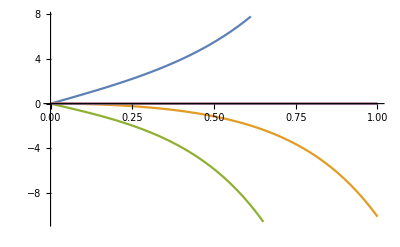

```mathematica
sr =Simplify[StateResponse[model,{UnitStep[t],UnitStep[t]},t]]
Plot[%,{t,0,1}]
```

```mathematica
ClearAll
```

ClearAll

```mathematica
A
```

A

```mathematica
p = {-2,-1+ⅈ,-1-ⅈ,-2.5+ⅈ,-2.5-ⅈ}
k=StateFeedbackGains[model,p]
```

{-2,-1+ⅈ,-1-ⅈ,-2.5+1. ⅈ,-2.5-1. ⅈ}

{{-0.134944,-3.71525,-0.913882,-0.137452,-0.125089},{0.00090514,-2.73949,-0.607007,0.177831,0.115767}}

```mathematica
k
```

k

```mathematica
model
```

0-7.994140004.148344.148340010000014.5727000-3.39541-3.3954100001.0000000-18.23518.235100000000000000000000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2351FalseFalseFalseAutomaticNone,{{x[t],0},{α[t],0},x_1,{θ[t],0},x_2},{{Tr[t],0},{Tl[t],0}},Automatic,t

```mathematica
p
```

p

```mathematica
<<ToMatlab`
k //ToMatlab
```

[(-0.134944E0),(-0.371525E1),(-0.913882E0),(-0.137452E0),( ...
  -0.125089E0);0.90514E-3,(-0.273949E1),(-0.607007E0),0.177831E0, ...
  0.115767E0];